# Pole friendly P_1 solver

## P_1 ODE Quadratic Solver

The IVP is
	y'' | = | f(z,y) | = | 6 y^2+z  with y(0)=y_0 and y'(0)=v_0
We can compute 
	y''(0)=6(y(0))^2+0=6 y_0^2
and approximate 
	y(h)≈y_0+h v_0+0.5 h^2 y''(0)=y_0+h v_0+0.5 h^2 y_0^2. 
Converting this to a fixed step size ODE solver is not too bad.  The first step is 
	y_1 | = | y_0+h v_0+0.5 h^2 y''(z_0)  | = | y_0+h v_0+0.5 h^2 f(z_0,y_0) 
v_1 | = | v_0+h v'(z_0)                             | = | v_0+h f(z_0,y_0)                           
The iteration (with a fixed step size h) is

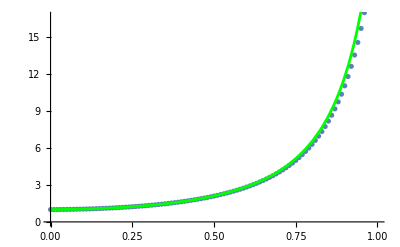

```mathematica
Clear[TwoStep]
TwoStep[h_][{zIn_,yIn_,vIn_}]:=Module[{y2d},
y2d=6 yIn^2+zIn;
 {zIn + h, yIn+h vIn + 0.5 h^2 y2d, vIn + h y2d}
]
{h,n}={0.01,100};
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=(n+1) h;
TwoData=NestList[TwoStep[h],{0,y0,v0},n];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
Show[
ListPlot[Re[TwoData⟦All,{1,2}⟧]],
Plot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green]
]
```

There are two obvious problems with this:  the step is not accurate enough and the algorithm has no mechanism to estimate or adjust h.  There is a more subtle problem: the real solution does not look at all like a polynomial.

## P_1 ODE Taylor Series Solver

The ODE is
	y''=6 y^2+z  with y(0)=y_0 and y'(0)=v_0
we can differentiate to get
	y''' | = | 12y y'+1
y'''' | = | 12(y y''+(y')^2)
y''''' | = | 12 (y y'''+3y' y'')
… |   |  
We can  compute as many derivatives as we want and construct the Taylor Series approximation
	y(h) | ≈ | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(0)	
this will presumably be more accurate than the quadratic approximation.

```mathematica
Clear[FiveStep]
FiveStep[h_][{zIn_,yIn_,vIn_}]:=Module[{y2d,y3d,y4d,y5d},
y2d=6 yIn^2+zIn;
y3d=12 yIn vIn+1;
y4d = 12(yIn y2d+vIn^2);
y5d = 12(yIn y3d + 3 vIn y2d);
 {zIn + h, 
yIn+h vIn + 0.5 h^2 y2d+1/(3!)h^3 y3d+1/(4!)h^4 y4d+1/(5!)h^5 y5d, 
vIn + h y2d + 0.5 h^2 y3d + 1/(3!)h^3 y4d+ 1/(4!)h^4 y5d}]
```

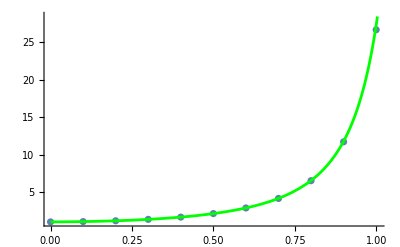

```mathematica
{h,n}={0.1,10};
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=(n+1) h;
FiveData=NestList[FiveStep[h],{0,y0,v0},n];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
Show[
ListPlot[Re[FiveData⟦All,{1,2}⟧]],
Plot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green],
PlotRange->All
]
```

Although each step is about 4 times as much work I can take ten times fewer steps and get a better answer!  The fancier algorithm should take about 4/10 the time.

## P_1 ODE Taylor Series Solver Step size control

The Taylor Series approximation
	y(h) | ≈ | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(0)	
comes with a built in approximate error estimate since
	y(h) | = | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(τ h)	
for some 0≤τ≤1.  The idea is that 
	1/(5!)h^5 y'''''(τ h)≈1/(5!)h^5 y'''''(0)
provides an error estimate for the fourth order polynomial
	y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) 
You can choose h so that the absolute tolerance 
	|1/(5!)h^5 y'''''(0)|<Tol
is satisfied.  You probably should choose h so that the relative tolerance
	(|1/(5!)h^5 y'''''(0)|)/y_0<Tol
is satisfied.  The logic of this probably argues for the quadratic update
	y_0+h v_0+1/2 h^2 y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) .
However, all practical code implementations use the higher order update.  This is called local extrapolation.  Step size control of this sort is always implemented with a safety factor called 0<γ<1 in the computation. For y the absolute error step size control looks like
	|1/(5!)h^5 y'''''(0)|=γ Tol | ⟹ | h=(γ (5!)/(|y'''''(0)|) )^(1/5).
For the derivative y' this looks like  
	|1/(4!)h^4 y'''''(0)|=γ Tol | ⟹h= | (γ (4!)/(|y'''''(0)|) )^(1/4)
You could work out where these switch over but there is no need.  A standard thing to do is to just take the smallest of these two step sizes. A maximum step size is also almost always imposed.

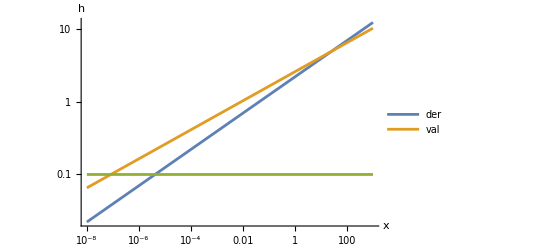

```mathematica
LogLogPlot[{(4! x)^(1/4),(5! x)^(1/5),0.1},{x,0.00000001, 1000},
PlotRange->All,
PlotLegends->{"der","val","max"},
AxesLabel->{"x","h"}
]
```

```mathematica
Clear[FiveStepTol]
FiveStepTol[Tol_][{zIn_,yIn_,vIn_}]:=Module[{y2d,y3d,y4d,y5d,h,γ=0.9},
y2d=6 yIn^2+zIn;
y3d=12 yIn vIn+1;
y4d = 12(yIn y2d+vIn^2);
y5d = 12(yIn y3d + 3 vIn y2d);
h = Min[0.1,(γ (4!)/Abs[y5d] )^(1/4),(γ (5!)/Abs[y5d] )^(1/5)];
 {zIn + h, 
yIn+h vIn + 0.5 h^2 y2d+1/(3!)h^3 y3d+1/(4!)h^4 y4d+1/(5!)h^5 y5d, 
vIn + h y2d + 0.5 h^2 y3d + 1/(3!)h^3 y4d+ 1/(4!)h^4 y5d}]
```

Now it is doing a good job of tracking the curve with small steps where needed.

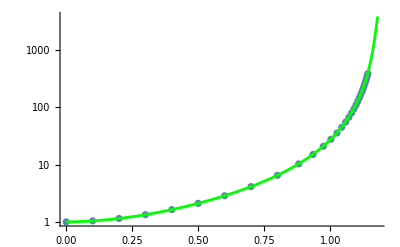

```mathematica
n=5;
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=1.18;
Tol=10.0^-14;
FiveData=NestList[FiveStepTol[Tol],{0,y0,v0},30];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
Show[
ListLogPlot[Re[FiveData⟦All,{1,2}⟧]],
LogPlot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All
]
```

Although each step is about 4 times as much work I can take ten times fewer steps and get a better answer!  The fancier algorithm should take about 4/10 the time.

## P_1 ODE Taylor Series Solver Target Interval and Step size control

The Taylor Series approximation
	y(h) | ≈ | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(0)	
comes with a built in approximate error estimate since
	y(h) | = | y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0)+1/(5!)h^5 y'''''(τ h)	
for some 0≤τ≤1.  The idea is that 
	1/(5!)h^5 y'''''(τ h)≈1/(5!)h^5 y'''''(0)
provides an error estimate for the fourth order polynomial
	y_0+h v_0+1/2 h^2y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) 
You can choose h so that the absolute tolerance 
	|1/(5!)h^5 y'''''(0)|<Tol
is satisfied.  You probably should choose h so that the relative tolerance
	(|1/(5!)h^5 y'''''(0)|)/y_0<Tol
is satisfied.  The logic of this probably argues for the quadratic update
	y_0+h v_0+1/2 h^2 y''(0)+1/(3!)h^3 y'''(0)+1/(4!)h^4 y''''(0) .
However, all practical code implementations use the higher order update.  This is called local extrapolation.  Step size control of this sort is always implemented with a safety factor called 0<γ<1 in the computation. For y the absolute error step size control looks like
	|1/(5!)h^5 y'''''(0)|=γ Tol | ⟹ | h=(γ (5!)/(|y'''''(0)|) )^(1/5).
For the derivative y' this looks like  
	|1/(4!)h^4 y'''''(0)|=γ Tol | ⟹h= | (γ (4!)/(|y'''''(0)|) )^(1/4)
You could work out where these switch over but there is no need.  A standard thing to do is to just take the smallest of these two step sizes. A maximum step size is also almost always imposed.

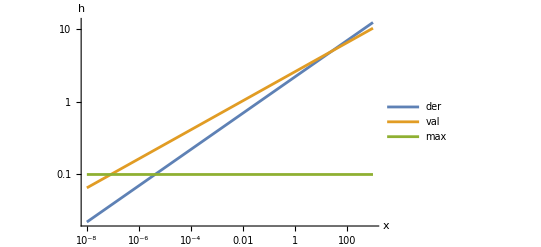

```mathematica
LogLogPlot[{(4! x)^(1/4),(5! x)^(1/5),0.1},{x,0.00000001, 1000},
PlotRange->All,
PlotLegends->{"der","val","max"},
AxesLabel->{"x","h"}
]
```

Our step size control Stepper for P_1 is

```mathematica
Clear[FiveStepTol]
FiveStepTol[Tol_][{zIn_,yIn_,vIn_}]:=Module[
{y2d,y3d,y4d,y5d,h,γ=0.9, MaxStep=0.1},
y2d=6 yIn^2+zIn;
y3d=12 yIn vIn+1;
y4d = 12(yIn y2d+vIn^2);
y5d = 12(yIn y3d + 3 vIn y2d);
h = Min[MaxStep,(γ (4!)/Abs[y5d] )^(1/4),(γ (5!)/Abs[y5d] )^(1/5)];
 {zIn + h, 
yIn+h vIn + 0.5 h^2 y2d+1/(3!)h^3 y3d+1/(4!)h^4 y4d+1/(5!)h^5 y5d, 
vIn + h y2d + 0.5 h^2 y3d + 1/(3!)h^3 y4d+ 1/(4!)h^4 y5d}]
```

All we need to do to make it useful is to run it up to a target maximum interval.

```mathematica
n=5;
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=1.18;
Tol=10.0^-10;
FiveData=NestWhileList[FiveStepTol[Tol],{0,y0,v0},(#⟦1⟧<TMax)&];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
TabView[{
"y"->Show[
ListLogPlot[Re[FiveData⟦All,{1,2}⟧],PlotRange->All],
LogPlot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]
],
"v"->Show[
ListLogPlot[Re[FiveData⟦All,{1,3}⟧],PlotRange->All],
LogPlot[Re[ySol'[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]]}]
```

12

This looks like it is working OK.  Here are some questions. What would happen to the step size if I made the error a relative error? Can we trust the solver Mathematica is using? What solver is Mathematica using? Can we change the solver Mathematica is using? Would we get the same answer in Julia, matlab, Python, etc?

## Pade Approximation vs Taylor Series: Big Picture

The analytical solution of P_1 has lots of double poles (but no branch cuts) in the complex plane.  The path we have been using along the real axis coms close to one of the poles. Here is the Taylor series solver running over the near pole.  To me it is amazing that it managed to track the solution through the “spike” at all!

```mathematica
{z0,y0,v0}={0,1+0.01 I, 0.1}; TMax=1.2;
Tol=10.0^-10;
FiveData=NestWhileList[FiveStepTol[Tol],{0,y0,v0},(#⟦1⟧<TMax)&];
ySol=NDSolveValue[{ y''[t]==6 y[t]^2+t, y[0]==y0,y'[0]==v0},y,{t, 0,TMax} ];
TabView[{
"y"->Show[
ListLogPlot[Re[FiveData⟦All,{1,2}⟧],PlotRange->All],
LogPlot[Re[ySol[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]
],
"v"->Show[
ListLogPlot[Re[FiveData⟦All,{1,3}⟧],PlotRange->All],
LogPlot[Re[ySol'[t]],{t,0, TMax},PlotStyle->Green,PlotRange->All],
PlotRange->All,
PlotLabel->Length[FiveData]]}]
```

12

If the real solution has a pole then maybe our approximate solution should have a pole!  The first thing we need to know how to do is produce a rational function that fits derivative data.  This is called a Pade approximant. https://en.wikipedia.org/wiki/Pad%C3%A9_approximant.  The Mathematica command is PadeApproximant. The improvement a rational approximation makes for an appropriate function is amazing!

```mathematica
Clear[f,t,z]
{n,m}={2,6}
f[z_]:=Sin[z]/(0.05+(z-0.5)^2) 
t[z_]=Normal[Series[f[z],{z,0,m+n}]];
p[z_]=PadeApproximant[f[z],{z,0,{m,n}}];
SetOptions[LogPlot,GridLines->Automatic,Frame->True];
TabView[{
"fun"->Plot[{f[z],t[z],p[z]},{z,0,2},PlotRange->{-2,12},
PlotLegends->{"f","t_(m + n)","p_(m/n)"}],
"err"->LogPlot[{Abs[f[z]-t[z]],Abs[f[z]-p[z]]},{z,0,2},
PlotLegends->{"|f-t_(m + n)|","|f-p_(m/n)|"}],
"rel err"->LogPlot[{Abs[1-t[z]/f[z]],Abs[1-p[z]/f[z]]},{z,0,2},
PlotLegends->{"|f-t_(m + n)|/|f|","|f-p_(m/n)|/|f|"}],
"errs p"->LogPlot[{Abs[1-p[z]/f[z]],Abs[f[z]-p[z]]},{z,0,2},
PlotLegends->{"|f-p_(m/n)|/|f|","|f-p_(m/n)|"}]
}]
```

{2,6}

1234

There is a copy of an article developing a specialized ODE solver for Painlevé transcendentals in the references directiory on GitHub. It is called PainleveFornbergOne.pdf

## Pade Approximation from Taylor Series: Computation

There are several ways to think about converting a rational function to and from a polynomial. We want 
	f(x)=c_0+x c_1+x^2 c_2+x^3 c_3+… ≈(a_0+x a_1+x^2 a_2+…)/(b_0+x b_1+x^2 b_2+…) 
and we can normalize the a and b components in some way.  Normalizing with b_0=1 is common  however other normalizations are also used. We choose how many c coefficients to compute and use.  Since there are (n+1)+(m+1)-1 independent coefficients in 
	 (a_0+x a_1+x^2 a_2+…+x^n a_n)/(b_0+x b_1+x^2 b_2+…+x^m b_m).
we should be able to match the first n+m+1 coefficients i.e. with b_0=1 
	c_0+x c_1+x^2 c_2+x^3 c_3+…+c_(n+m)x^(n+m)+…=(a_0+x a_1+x^2 a_2+…+x^n a_n)/(1+x b_1+x^2 b_2+…+x^m b_m)
Cross multiplying to remove the fraction gives
	(∑_(i=0)^(m+n) c_i x^i+O(x^(m+n+1)))(b_0+∑_(i=1)^m b_i x^i)=∑_(i=0)^n a_i x^i+∑_(i=n+1)^(n+m) 0 x^i
for the unnormalized version.This is just a set of linear equations relating the coefficient vectors a and b. The Pade article by Trefethen et al in the references provides a detailed of the derivation for m≥n of the linear system with a_(m+1)=a_(m+2)=…=a_(m+n)=0.
-Graphics-
The way to interpret this computationally is: b is any non-trivial element of the null space of the bottom (n)×(n+1) matrix; and the non zero portion of a is computed by simply multiplying that b by the top matrix.  In the Pade paper the normalization is |b|=1.  This is straight forward to implement. Here is an implementation and brief test.

```mathematica
TtoP[cs_,n_]:= Module[{m,as,bs,CMat},
m=Length[cs]-n-2;
CMat=LowerTriangularize[ToeplitzMatrix[cs]];
{bs}=NullSpace[CMat⟦m+2;;m+n+1,1;;n+1⟧];
as=CMat⟦1;;m+1,1;;n+1⟧.bs;
{as,bs}]
P[{as_,bs_}][z_]:=(as.Table[z^i,{i,0,Length[as]-1}])/(bs.Table[z^i,{i,0,Length[bs]-1}]);
```

{1.84147,1.5403,-1.19089,-0.502648,0.629132,0.673448,-0.483331,-0.826075,0.52132}

{1.84147,1.5403,-1.19089,-0.502648,0.629132,0.673448,-0.483331,-0.826075,0.521312}

{1.84147,1.5403,-1.19089,-0.502648,0.629132,0.673448,-0.483331,-0.826075,0.521312,0.84631}

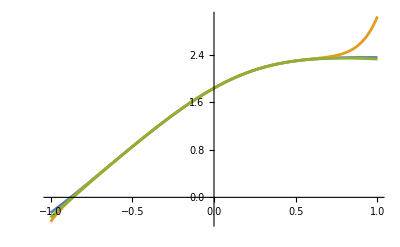

```mathematica
{n,m}={3,5};
f[z_]:= Sin[z+Cos[z]]+E^z/(1.0+z^2)
t[z_]=Normal[Series[f[z],{z,0,n+m+1}]];
cs=Table[(Derivative[i][f][0])/(i!),{i,0,n+m+1}];
{as,bs}=TtoP[cs,n];
CoefficientList[Series[P[{as,bs}][z],{z, 0,n+m}],z]
CoefficientList[Series[f[z],{z, 0,n+m}],z]
CoefficientList[t[z],z]
Plot[{f[z],t[z],P[{as,bs}][z]},{z,-1,1}]
```

## High Order Taylor Series: Demo

Here is a demo on the first step of our P_1 problem.  The first thing to do is compute more derivatives of the ODE 
	y''==6 y^2+z
We could do this manually but I had the computer do it for me

```mathematica
Clear[p,y,z]
p[z_]:=6 y[z]^2+z
MaxOrder=15;
TableForm[
DerComp=Table[
p[z_]=D[p[z],z];
Simplify[p[z]/.{y[z]->yd[0],Derivative[i_][y][z]:>yd[i]}],
{j,1,MaxOrder-2}],
TableHeadings->{Table[yd[i],{i,3,MaxOrder}],Automatic}]
```

yd[3] | 1+12 yd[0] yd[1]
yd[4] | 12 (yd[1]^2+yd[0] yd[2])
yd[5] | 12 (3 yd[1] yd[2]+yd[0] yd[3])
yd[6] | 12 (3 yd[2]^2+4 yd[1] yd[3]+yd[0] yd[4])
yd[7] | 12 (10 yd[2] yd[3]+5 yd[1] yd[4]+yd[0] yd[5])
yd[8] | 12 (10 yd[3]^2+15 yd[2] yd[4]+6 yd[1] yd[5]+yd[0] yd[6])
yd[9] | 12 (35 yd[3] yd[4]+21 yd[2] yd[5]+7 yd[1] yd[6]+yd[0] yd[7])
yd[10] | 12 (35 yd[4]^2+56 yd[3] yd[5]+28 yd[2] yd[6]+8 yd[1] yd[7]+yd[0] yd[8])
yd[11] | 12 (126 yd[4] yd[5]+84 yd[3] yd[6]+36 yd[2] yd[7]+9 yd[1] yd[8]+yd[0] yd[9])
yd[12] | 12 (126 yd[5]^2+210 yd[4] yd[6]+120 yd[3] yd[7]+45 yd[2] yd[8]+10 yd[1] yd[9]+yd[0] yd[10])
yd[13] | 12 (462 yd[5] yd[6]+330 yd[4] yd[7]+165 yd[3] yd[8]+55 yd[2] yd[9]+11 yd[1] yd[10]+yd[0] yd[11])
yd[14] | 12 (462 yd[6]^2+792 yd[5] yd[7]+495 yd[4] yd[8]+220 yd[3] yd[9]+66 yd[2] yd[10]+12 yd[1] yd[11]+yd[0] yd[12])
yd[15] | 12 (1716 yd[6] yd[7]+1287 yd[5] yd[8]+715 yd[4] yd[9]+286 yd[3] yd[10]+78 yd[2] yd[11]+13 yd[1] yd[12]+yd[0] yd[13])

```mathematica
Clear[FifteenStepTayTol]
FifteenStepTayTol[Tol_][{zIn_,yIn_,vIn_}]:=Module[{yd,DerComp,MaxStep=1.0,γ=0.9},
DerComp={1+12 yd[0] yd[1],12 (yd[1]^2+yd[0] yd[2]),12 (3 yd[1] yd[2]+yd[0] yd[3]),12 (3 yd[2]^2+4 yd[1] yd[3]+yd[0] yd[4]),12 (10 yd[2] yd[3]+5 yd[1] yd[4]+yd[0] yd[5]),12 (10 yd[3]^2+15 yd[2] yd[4]+6 yd[1] yd[5]+yd[0] yd[6]),12 (35 yd[3] yd[4]+21 yd[2] yd[5]+7 yd[1] yd[6]+yd[0] yd[7]),12 (35 yd[4]^2+56 yd[3] yd[5]+28 yd[2] yd[6]+8 yd[1] yd[7]+yd[0] yd[8]),12 (126 yd[4] yd[5]+84 yd[3] yd[6]+36 yd[2] yd[7]+9 yd[1] yd[8]+yd[0] yd[9]),12 (126 yd[5]^2+210 yd[4] yd[6]+120 yd[3] yd[7]+45 yd[2] yd[8]+10 yd[1] yd[9]+yd[0] yd[10]),12 (462 yd[5] yd[6]+330 yd[4] yd[7]+165 yd[3] yd[8]+55 yd[2] yd[9]+11 yd[1] yd[10]+yd[0] yd[11]),12 (462 yd[6]^2+792 yd[5] yd[7]+495 yd[4] yd[8]+220 yd[3] yd[9]+66 yd[2] yd[10]+12 yd[1] yd[11]+yd[0] yd[12]),12 (1716 yd[6] yd[7]+1287 yd[5] yd[8]+715 yd[4] yd[9]+286 yd[3] yd[10]+78 yd[2] yd[11]+13 yd[1] yd[12]+yd[0] yd[13])};
{yd[0],yd[1]}={yIn,vIn};yd[2]=6 yd[0]^2+zIn;
Do[
yd[i+2]=DerComp⟦i⟧,
{i, Length[DerComp]}];
h = Min[MaxStep,(γ (14!)/Abs[yd[15]] )^(1/14),(γ (15!)/Abs[yd[15]] )^(1/15)];
 {zIn + h, 
Sum[yd[i]/(i!) h^i,{i,0, Length[DerComp]+2}],
 Sum[yd[i]/((i-1)!) h^(i-1),{i,1, Length[DerComp]+2}]
}]
```

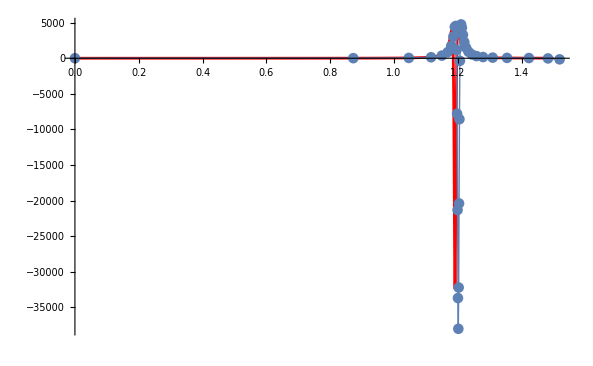

```mathematica
h=0.1;
{z0,y0,v0}={0,1+1/100 I, 1/10};
Tol=10^-10; zMax=1.5;
ySol=NDSolveValue[{y''[z]==6 y[z]^2+z, y[0]==y0,y'[0]==v0},y, {z, 0, zMax},WorkingPrecision->64,PrecisionGoal->16,MaxSteps->10^7];
zyvData=NestWhileList[FifteenStepTayTol[Tol],{z0,y0,v0},(#⟦1⟧<1.5)&];
Show[
Plot[Re[ySol[z]],{z,0, zMax},PlotRange->All,PlotStyle->Red],
ListPlot[Re[zyvData⟦All,{1,2}⟧],
PlotRange->All,PlotStyle->Thin,
Joined->True,Mesh->All,
PlotLabel->Length[zyvData]]
]
```

The questions are: Would Pade steps do much better than the Taylor steps? How should we decide how big a Pade step we can take?  What could we possibly compare our Pade solver to?

## High Order Taylor Series: Demo

Here is a demo on the P_1 problem.  The first thing to do is compute more derivatives of the ODE 
	y''==6 y^2+z
We could do this manually but I had the computer do it for me

```mathematica
Clear[p,y,z]
p[z_]:=6 y[z]^2+z
MaxOrder=15;
TableForm[
DerComp=Table[
p[z_]=D[p[z],z];
Simplify[p[z]/.{y[z]->yd[0],Derivative[i_][y][z]:>yd[i]}],
{j,1,MaxOrder-2}],
TableHeadings->{Table[yd[i],{i,3,MaxOrder}],Automatic}]
```

yd[3] | 1+12 yd[0] yd[1]
yd[4] | 12 (yd[1]^2+yd[0] yd[2])
yd[5] | 12 (3 yd[1] yd[2]+yd[0] yd[3])
yd[6] | 12 (3 yd[2]^2+4 yd[1] yd[3]+yd[0] yd[4])
yd[7] | 12 (10 yd[2] yd[3]+5 yd[1] yd[4]+yd[0] yd[5])
yd[8] | 12 (10 yd[3]^2+15 yd[2] yd[4]+6 yd[1] yd[5]+yd[0] yd[6])
yd[9] | 12 (35 yd[3] yd[4]+21 yd[2] yd[5]+7 yd[1] yd[6]+yd[0] yd[7])
yd[10] | 12 (35 yd[4]^2+56 yd[3] yd[5]+28 yd[2] yd[6]+8 yd[1] yd[7]+yd[0] yd[8])
yd[11] | 12 (126 yd[4] yd[5]+84 yd[3] yd[6]+36 yd[2] yd[7]+9 yd[1] yd[8]+yd[0] yd[9])
yd[12] | 12 (126 yd[5]^2+210 yd[4] yd[6]+120 yd[3] yd[7]+45 yd[2] yd[8]+10 yd[1] yd[9]+yd[0] yd[10])
yd[13] | 12 (462 yd[5] yd[6]+330 yd[4] yd[7]+165 yd[3] yd[8]+55 yd[2] yd[9]+11 yd[1] yd[10]+yd[0] yd[11])
yd[14] | 12 (462 yd[6]^2+792 yd[5] yd[7]+495 yd[4] yd[8]+220 yd[3] yd[9]+66 yd[2] yd[10]+12 yd[1] yd[11]+yd[0] yd[12])
yd[15] | 12 (1716 yd[6] yd[7]+1287 yd[5] yd[8]+715 yd[4] yd[9]+286 yd[3] yd[10]+78 yd[2] yd[11]+13 yd[1] yd[12]+yd[0] yd[13])

```mathematica
Clear[FifteenStepTayTol]
FifteenStepTayTol[Tol_][{zIn_,yIn_,vIn_}]:=Module[{yd,DerComp,MaxStep=1.0,γ=0.9},
DerComp={1+12 yd[0] yd[1],12 (yd[1]^2+yd[0] yd[2]),12 (3 yd[1] yd[2]+yd[0] yd[3]),12 (3 yd[2]^2+4 yd[1] yd[3]+yd[0] yd[4]),12 (10 yd[2] yd[3]+5 yd[1] yd[4]+yd[0] yd[5]),12 (10 yd[3]^2+15 yd[2] yd[4]+6 yd[1] yd[5]+yd[0] yd[6]),12 (35 yd[3] yd[4]+21 yd[2] yd[5]+7 yd[1] yd[6]+yd[0] yd[7]),12 (35 yd[4]^2+56 yd[3] yd[5]+28 yd[2] yd[6]+8 yd[1] yd[7]+yd[0] yd[8]),12 (126 yd[4] yd[5]+84 yd[3] yd[6]+36 yd[2] yd[7]+9 yd[1] yd[8]+yd[0] yd[9]),12 (126 yd[5]^2+210 yd[4] yd[6]+120 yd[3] yd[7]+45 yd[2] yd[8]+10 yd[1] yd[9]+yd[0] yd[10]),12 (462 yd[5] yd[6]+330 yd[4] yd[7]+165 yd[3] yd[8]+55 yd[2] yd[9]+11 yd[1] yd[10]+yd[0] yd[11]),12 (462 yd[6]^2+792 yd[5] yd[7]+495 yd[4] yd[8]+220 yd[3] yd[9]+66 yd[2] yd[10]+12 yd[1] yd[11]+yd[0] yd[12]),12 (1716 yd[6] yd[7]+1287 yd[5] yd[8]+715 yd[4] yd[9]+286 yd[3] yd[10]+78 yd[2] yd[11]+13 yd[1] yd[12]+yd[0] yd[13])};
{yd[0],yd[1]}={yIn,vIn};yd[2]=6 yd[0]^2+zIn;
Do[
yd[i+2]=DerComp⟦i⟧,
{i, Length[DerComp]}];
h = Min[MaxStep,(γ (14!)/Abs[yd[15]] )^(1/14),(γ (15!)/Abs[yd[15]] )^(1/15)];
 {zIn + h, 
Sum[yd[i]/(i!) h^i,{i,0, Length[DerComp]+2}],
 Sum[yd[i]/((i-1)!) h^(i-1),{i,1, Length[DerComp]+2}]
}]
```

```mathematica
h=0.1;
{z0,y0,v0}={0,1+1/100 I, 1/10};
Tol=10^-10; zMax=1.5;
ySol=NDSolveValue[{y''[z]==6 y[z]^2+z, y[0]==y0,y'[0]==v0},y, {z, 0, zMax},WorkingPrecision->64,PrecisionGoal->16,MaxSteps->10^7];
zyvData=NestWhileList[FifteenStepTayTol[Tol],{z0,y0,v0},(#⟦1⟧<1.5)&];
Show[
Plot[Re[ySol[z]],{z,0, zMax},PlotRange->All,PlotStyle->Red],
ListPlot[Re[zyvData⟦All,{1,2}⟧],
PlotRange->All,PlotStyle->Thin,
Joined->True,Mesh->All,
PlotLabel->Length[zyvData]]
]
```

-Graphics-

The questions are: Would Pade steps do much better than the Taylor steps? How should we decide how big a Pade step we can take?  What could we possibly compare our Pade solver to?